## Energy Levels - 135Pr (2023 implementation)

```mathematica
ClearAll["Global`*"]
```

```mathematica
spin0={7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5};
spin1={8.5,10.5,12.5,14.5,16.5};
spin2={9.5,11.5,13.5,15.5};
band1exp={0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069};
band1th={0.6489231303332899,1.3416115046837764,2.0786652448783793,2.860331759974865,3.6867336223178806,4.557939039239063,5.473989176901558,6.434910428394987,7.440720528273122,8.491431849871653,9.587053296875014};
band2exp={0.7466,1.4731,2.2688,3.2245,4.3362};
band2th={0.9897459594242473,1.7045729395035516,2.4639124739781493,3.26793566451142,4.116732866147538};
band3exp={1.1971,2.0237,2.7875,3.7965};
band3th={1.257638840232143,2.0279506060426935,2.841912394589692,3.7000375108632677};
```

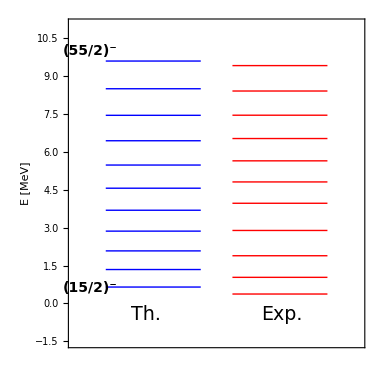

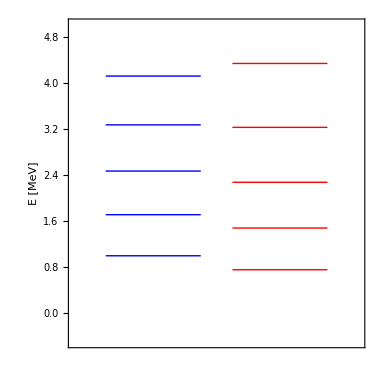

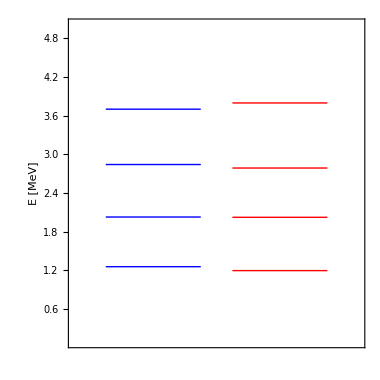

```mathematica
levelplot[band_,shift_,color_]:=ListLinePlot[Table[{{shift,band[[i]]},{shift+3,band[[i]]}},{i,1,Length[band]}]
,Frame->True,Axes->False,FrameTicks->{{Automatic,Automatic},{None,None}},FrameLabel->{{"E [MeV]",None},{None,None}},
PlotStyle->Directive[{color,Thick}],
FrameStyle->Directive[Black,Thick],
LabelStyle->{21,Black,FontFamily->"Latin Modern Roman"},
ImageSize->380];
(* BAND B1 *)
Show[levelplot[band1th,1,Blue],levelplot[band1exp,5,Red],PlotRange->{{0,9},{-1.5,11}},AspectRatio->1, Epilog->{Inset[Style["(15/2)^-",Black,Bold,FontFamily->"Latin Modern Roman",14],{0.5,0.6}],Inset[Style["(55/2)^-",Black,Bold,FontFamily->"Latin Modern Roman",14],{0.5,10}],Inset[Style["Th.",Black,Italic,19,FontFamily->"Latin Modern Roman"],Scaled[{0.26,0.1}]],
Inset[Style["Exp.",Black,Italic,19,FontFamily->"Latin Modern Roman"],Scaled[{0.72,0.1}]]
}]
(* BAND B2 *)
Show[levelplot[band2th,1,Blue],levelplot[band2exp,5,Red],PlotRange->{{0,9},{-0.5,5}},AspectRatio->1]
(* BAND B3 *)
Show[levelplot[band3th,1,Blue],levelplot[band3exp,5,Red],PlotRange->{{0,9},{0.1,5}},AspectRatio->1]
```